# Magnetogenesis

## Parameters

Ratio of the eigenvalues of kinetic mixing

```mathematica
r  =  0.01;
```

The initial value of the initial rescaled conformal time

```mathematica
Subscript[y, in]  =  -100.0;
```

The final value of the rescaled conformal time

```mathematica
Subscript[y, out]  =  -10^-10;
```

## Definitions

A shorthand for the identity matrix

```mathematica
II  =  ({{1, 0}, {0, 1}});
```

The Hubble constant during inflation (GeV)  — not currently used

```mathematica
H  =  10^13;
```

The co-moving momentum as the function of the final conformal time (in the units of the Hubble constant)

```mathematica
k  =  (- Subscript[y, out]);
```

The scale factor of the universe at the end of inflation, is normalized to be one

```mathematica
a  =  1.0;
```

The variable that enters the cosine / sine in the mass matrix

```mathematica
ζ̂  =  ( r + 1/r ) Log [ Subscript[y, in]/y];
```

The rescaled mass matrix

```mathematica
Q  = ( 1  -  1/y^2 ( r - 1/r )^2/4) II  -  1/y^2 (r - 1/r)/2 √(r^2 + 1/r^2 + 3)  ({{Cos[ζ̂], Sin[ζ̂]}, {Sin[ζ̂], - Cos[ζ̂]}});
```

The initial value of the function

```mathematica
Subscript[Ψ, in]   = II;
```

## Equations

Evolution equation

```mathematica
evolution  =  {     Ψ''[y]    +    Q . Ψ[y]    ==    0,
                                Ψ[Subscript[y, in]]  ==    Subscript[Ψ, in],
                                Ψ'[Subscript[y, in]]  ==  - ⅈ  Subscript[Ψ, in]                   };
```

## Solution

Solving the differential equation

```mathematica
solution = NDSolve[    evolution,    Ψ,    { y, Subscript[y, in], Subscript[y, out]},    MaxSteps->Infinity    ]
```

{{Ψ→InterpolatingFunction[{{-100.,-1.×10^-10}},<>]}}

The value where to plot starting from

```mathematica
Subscript[y, left]  =   4 Subscript[y, out];
```

```mathematica
Plot[    {  Abs[    (  Ψ[y] /. solution  )  [[1,1,1]]    ] },    {  y,  Subscript[y, left],  Subscript[y, out]  }    ]
```

-Graphics-

```mathematica
Plot[    {  Abs[    (  Ψ[y] /. solution  )  [[1,1,2]]    ] },    {  y,  Subscript[y, left],  Subscript[y, out]  }    ]
```

-Graphics-

```mathematica
Plot[    {  Abs[    (  Ψ[y] /. solution  )  [[1,2,1]]    ] },    {  y,  Subscript[y, left],  Subscript[y, out]  }    ]
```

-Graphics-

```mathematica
Plot[    {  Abs[    (  Ψ[y] /. solution  )  [[1,2,2]]    ] },    {  y,  Subscript[y, left],  Subscript[y, out]  }    ]
```

-Graphics-

## Power Spectrum for the Magnetic Field

Parameter entering the diagonalization matrices (matrix Δ in my notations)

```mathematica
ρ  =  ArcSin[ 1/(√(r^2 + 1/r^2 + 3))];
```

Parameter of the rotation in the rotation matrix

```mathematica
s  =  1/2( r + 1/r ) Log[Subscript[y, in]/Subscript[y, out]]    -    1/2 ρ;
```

Rotation matrix which removes the one-derivative terms

```mathematica
R  =  ({{Cos[s], -Sin[s]}, {Sin[s], Cos[s]}});
```

Power Spectrum

```mathematica
P[Ψ_, α_] := 1/(2 π^2)(k/a)^4 (    Re[  (  Rᵀ . Ψ . Ψ† . Conjugate[R]  )[[ α, α ]]  ]    )
```

We denote the solution itself with the letter Ξ

```mathematica
Ξ[y_]  :=  Evaluate[  Ψ[y]  /.  solution  ][[1]];
```

Calculate the Power Spectrum

```mathematica
{  P[  Ξ[Subscript[y, out]], 1],  P[  Ξ[Subscript[y, out]], 2]  }
```

{9.46671×10^92,7.38161×10^90}

```mathematica
{{Subscript[y, out] ( r  =  0.01 ), Subscript[P, 1]}, {1, 3.204731117930963*^118}, {10^-1, 4.73975970955288*^126}, {10^-2, 2.542258347979342*^126}, {10^-3, 2.261905818521859*^122}, {10^-4, 6.746694573978996*^118}, {10^-5, 3.9524401206701496*^114}, {10^-6, 7.315360566665372*^107}, {10^-7, 3.999544820233466*^106}, {10^-8, 8.403603047891249*^102}, {10^-9, 3.8449125427440685*^98}, {10^-10, 9.466713119129096*^92}};
```

```mathematica
Pr01  =  {{1, 3.204731117930963*^118}, 
{10^(-1), 4.73975970955288*^126}, 
{10^(-2), 2.542258347979342*^126}, 
  {10^(-3), 2.261905818521859*^122}, 
{10^(-4), 6.746694573978996*^118}, 
  {10^(-5), 3.9524401206701496*^114}, 
{10^(-6), 7.315360566665372*^107}, 
  {10^(-7), 3.999544820233466*^106}, 
{10^(-8), 8.403603047891249*^102}, 
{10^(-9), 3.8449125427440685*^98}, 
  {10^(-10), 9.466713119129096*^92}};
```

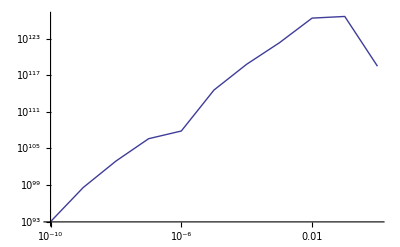

```mathematica
ListLogLogPlot[ Pr01, Joined->True ]
```